## Analyzing the runtime of the prime? procedure

The primality of a given number can be tested with the following three procedures:

(define (divides? a b) (= (remainder b a) 0))

(define (prime? n)
  (define (smallest-divisor n) (find-divisor n 2))
  (define (find-divisor n test-divisor)
    (cond ((> (square test-divisor) n) n)
          ((divides? test-divisor n) test-divisor)
          (else (find-divisor n (+ test-divisor 1)))))
  (= n (smallest-divisor n)))

(define (fast-prime? n)
  (define (smallest-divisor n) (find-divisor n 2))
  (define (find-divisor n test-divisor)
    (cond ((> (square test-divisor) n) n)
          ((divides? test-divisor n) test-divisor)
          (else (find-divisor n (next test-divisor)))))
  (define (next test)
    (if (= test 2)
        3
        (+ test 2))) ; avoid repeating divisors of two
  (= n (smallest-divisor n)))

(define (fermat-prime? n times)
  (define (fermat-test n)
    (check (+ 1 (random (- n 1))) n))
  (define (check a n)
    (= (expmod a n n) a))
  (define (expmod base exp m) ; base ^ exp modulo m
    (cond ((= exp 0) 1)
          ((even? exp) (remainder
                         (square (expmod base
                                         (/ exp 2)
                                         m))
                         m))
          (else (remainder
                  (* base (expmod base (- exp 1) m))
                  m))))

  (cond ((= times 0) true) ; at this point the test hasn’t failed so we’ll assume it’s prime
        ((fermat-test n) (fermat-prime? n (- times 1)))
        (else false))) ; nope

Below is runtime data for these primality tests for 1000 random 10-digit primes:

```mathematica
t=Import[NotebookDirectory[]<>"runtimes.csv"];
prime={#[[1]],#[[2]]}&/@t;
fastPrime={#[[1]],#[[3]]}&/@t;
fermatPrime={#[[1]],#[[4]]}&/@t;
```

Since the prime? (and fast-prime?) procedure has a runtime complexity of Θ(√n), the runtimes should approximately fit a square root function:

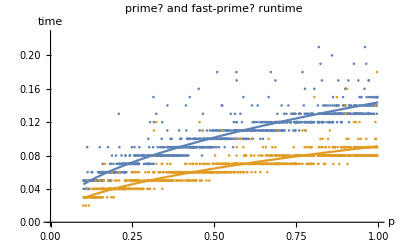

```mathematica
sqrtModel=a Sqrt[x];
primeModel[x_]=sqrtModel/.FindFit[prime,sqrtModel,{{a,1.5 10^-6(*starting value that worked on my computer*)}},x];fastPrimeModel[x_]=sqrtModel/.FindFit[fastPrime,sqrtModel,{{a,0.7 10^-6}},x];
Show[ListPlot[{prime,fastPrime},PlotLabel->"prime? and fast-prime? runtime",AxesLabel->{"p","time"}],Plot[{primeModel[x],fastPrimeModel[x]},{x,10^9,10^10}]]
```

Note that horizontal banding, which is a result the limited decimal precision of the (runtime) procedure (two decimal points). However, the general distribution should give the idea that the runtimes do fit

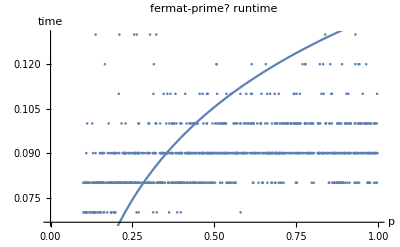

```mathematica
logModel=a Log[x]+b;(*Simplification of a Log[b x] but that gives errors*)
fermatPrimeModel[x_]=logModel/.FindFit[prime,logModel,{a,b},x];
Show[ListPlot[fermatPrime,PlotLabel->"fermat-prime? runtime",AxesLabel->{"p","time"}],Plot[fermatPrimeModel[x],{x,10^9,10^10}]]
```

Since fermat-prime? has a very small runtime, data is a bit fuzzy here, but fitting to a logarithmic function approximately works.

#### Approximation errors

```mathematica
ListPlot[Function[model,{#[[1]],#[[2]]-model[[1]][#[[1]]]}&/@model[[2]]]/@{{primeModel,prime},{fastPrimeModel,fastPrime},{fermatPrimeModel,fermatPrime}},PlotLabel->"Approximation Error (by value)",PlotLabels->{"prime?","fast-prime?","fermat-prime?"}]
```

-Graphics-

Note that there is some diagonal banding here. I suspect that this is caused by the horizontal banding from the limited precision of timing from earlier.
Also fermat-prime? is way off because of precision problems with recording runtime.

#### Generating more Data

The data was generated in multiple steps. First call RandomPrime[{10^10,10^11},n] (12-digit prime numbers; depending on the speed of your machine you may want to adjust this for speed), where n is the desired number of data points. Copy the output into some editor with RegEx support (very helpful), then search-and replace \{?(\d+)(\}|(, (\\\n)?)?) with (timed-prime-test $1)\n. Now switch over to the shell and cd to the location of the Scheme source file. Call cat <source>.scm - | scheme | tee out.txt, which will load the program into scheme, with output being copied to out.txt. Paste the scheme commands, and after execution and termination the log of the scheme session will be copied to out.txt. The output will contain the actual data along with a bunch of junk. How to convert this into CSV format is left as an exercise to the reader.